```mathematica
A DsixTools Program
This notebook loads DsixTools and shows how to use the SMEFTrunner, EWmatcher and WETrunner modules.
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Start DsixTools

```mathematica
Needs["DsixTools`"]
```

DsixTools 1.0

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.XXXXX

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

## Read input files

```mathematica
ReadInputFiles["Options.dat","WCsInput.dat","SMInput.dat"];
```

Input: SMEFT Wilson coefficients

## Load SMEFTrunner module

```mathematica
LoadModule["SMEFTrunner"]
```

SMEFTrunner

DsixTools module for the RGE running of the Standard Model Effective Theory

## Use SMEFTrunner module

```mathematica
LoadBetaFunctions;
```

Loading SMEFT β functions

```mathematica
RunRGEsSMEFT;
```

Running

Running finished!

## Results after SMEFTrunner

```mathematica
(* The results obtained with SMEFT runner are saved in 'Var/.run', which can be evaluated at different t=Log[μ] values *)
```

```mathematica
PrintResults=False;
If[PrintResults,
Print[outSMEFTrunner/.t->tHIGH];
Print[outSMEFTrunner/.t->Log[10,Sqrt[LOWSCALE*HIGHSCALE]]];
Print[outSMEFTrunner/.t->tLOW];
];
```

```mathematica
(* The results can also be plotted as a function of the energy scale *)
```

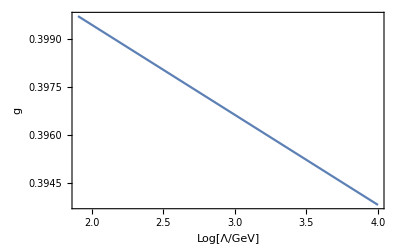
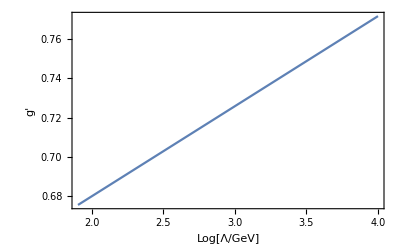
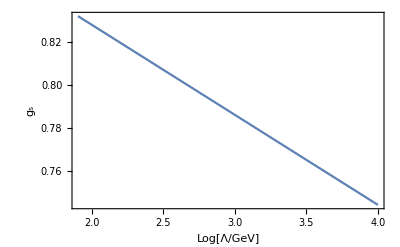

```mathematica
(* Gauge couplings *)
plotGauge1=Plot[outSMEFTrunner[[1]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g",None,None}];
plotGauge2=Plot[outSMEFTrunner[[2]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g'",None,None}];
plotGauge3=Plot[outSMEFTrunner[[3]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g_s",None,None}];
plotGauge={plotGauge1,plotGauge2,plotGauge3}
```

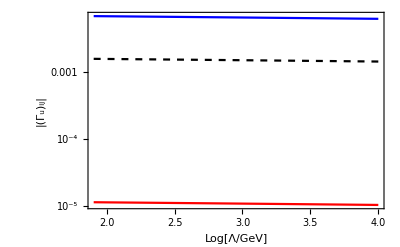

```mathematica
(* Yukawa couplings *)
plotYukawa1=LogPlot[Abs[outSMEFTrunner[[6]]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","|(Γ_u)_11|",None,None},PlotStyle->Red];
plotYukawa2=LogPlot[Abs[outSMEFTrunner[[7]]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","|(Γ_u)_12|",None,None},PlotStyle->{Black,Dashed}];
plotYukawa3=LogPlot[Abs[outSMEFTrunner[[10]]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","|(Γ_u)_22|",None,None},PlotStyle->Blue];
Show[{plotYukawa1,plotYukawa2,plotYukawa3},PlotRange->{All,All},FrameLabel->{"Log[Λ/GeV]","|(Γ_u)_ij|",None,None}]
```

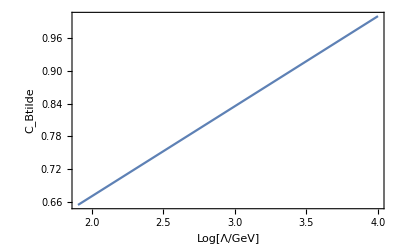
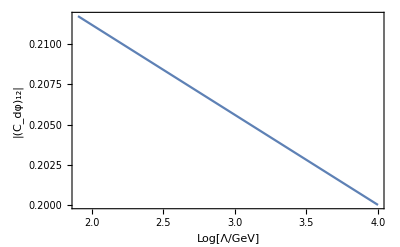
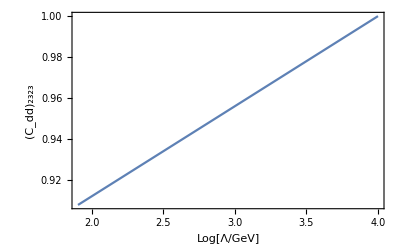

```mathematica
(* Wilson coefficients *)
plotWC1=Plot[outSMEFTrunner[[48]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","C_Btilde",None,None}];
plotWC2=Plot[Abs[outSMEFTrunner[[61]]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","|(C_dφ)_12|",None,None}];
plotWC3=Plot[outSMEFTrunner[[443]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","(C_dd)_2323",None,None}];
plotWC={plotWC1,plotWC2,plotWC3}
```

```mathematica
(* One can also export the t dependence of the WCs as follows: *)
exportMany=False;
outMany="Output/cGzero-ND.dat";
If[exportMany,
nPoints=100;
tInt=Table[tLOW+(tHIGH-tLOW)(i-1)/(nPoints-1),{i,1,nPoints}];
dataexport=Table[outSMEFTrunner[[j]]/.t->tInt[[i]],{i,1,nPoints},{j,0,Length[Var]}];
dataexport[[All,1]]=tInt;
Export[outMany,dataexport];
];
```

```mathematica
(* Finally, one can also export the results to a file *)
```

```mathematica
ExportSMEFTrunner;
```

Exporting SMEFTrunner results

## Load EWmatcher module

```mathematica
LoadModule["EWmatcher"]
```

EWmatcher

DsixTools module for the matching at the electroweak scale

## Use EWmatcher module

```mathematica
RotateToMassBasis;
```

Rotating SMEFT WCs to mass basis

```mathematica
ApplyEWmatching;
```

Matching to low energy operators

## Results after EWmatcher

```mathematica
(* One can print the resulting SM WCs in the mass basis *)
```

```mathematica
DD[1,1,2,2]/.ToMassBasis
```

7.97456×10^-7+0. ⅈ

```mathematica
Cddtilde
```

{{{{2.1214×10^-7+1.32349×10^-23 ⅈ,-1.00331×10^-6-1.82589×10^-6 ⅈ,-0.0000186014-4.38986×10^-6 ⅈ},{-1.00331×10^-6+1.82589×10^-6 ⅈ,7.97456×10^-7+0. ⅈ,0.000307157-0.000108157 ⅈ},{-0.0000186014+4.38986×10^-6 ⅈ,0.000307157+0.000108157 ⅈ,-1.0096×10^-6+0. ⅈ}},{{-1.00331×10^-6-1.82589×10^-6 ⅈ,-3.18711×10^-7+0.0000337993 ⅈ,-0.0000218609+0.0000114941 ⅈ},{7.97456×10^-7+0. ⅈ,-0.0000263624+0.0000345706 ⅈ,0.000204193-0.000362919 ⅈ},{0.000307157+0.000108157 ⅈ,-0.00341079-0.00437204 ⅈ,0.0000273657-0.0000327447 ⅈ}},{{-0.0000186014-4.38986×10^-6 ⅈ,-0.0000218609+0.0000114941 ⅈ,0.00193631+0.0024466 ⅈ},{0.000307157-0.000108157 ⅈ,0.000204193-0.000362919 ⅈ,-0.0502383-0.0172982 ⅈ},{-1.0096×10^-6+1.27055×10^-21 ⅈ,0.0000273657-0.0000327447 ⅈ,-0.000185592+0.000367309 ⅈ}}},{{{-1.00331×10^-6+1.82589×10^-6 ⅈ,7.97456×10^-7+4.23516×10^-22 ⅈ,0.000307157-0.000108157 ⅈ},{-3.18711×10^-7-0.0000337993 ⅈ,-0.0000263624-0.0000345706 ⅈ,-0.00341079+0.00437204 ⅈ},{-0.0000218609-0.0000114941 ⅈ,0.000204193+0.000362919 ⅈ,0.0000273657+0.0000327447 ⅈ}},{{7.97456×10^-7+4.23516×10^-22 ⅈ,-0.0000263624+0.0000345706 ⅈ,0.000204193-0.000362919 ⅈ},{-0.0000263624-0.0000345706 ⅈ,-0.000110268+1.69407×10^-21 ⅈ,0.000399543+0.00707914 ⅈ},{0.000204193+0.000362919 ⅈ,0.000399543-0.00707914 ⅈ,0.00010947-8.47033×10^-22 ⅈ}},{{0.000307157-0.000108157 ⅈ,0.000204193-0.000362919 ⅈ,-0.0502383-0.0172982 ⅈ},{-0.00341079+0.00437204 ⅈ,0.000399543+0.00707914 ⅈ,0.879286-0.213393 ⅈ},{0.0000273657+0.0000327447 ⅈ,0.00010947-2.5411×10^-21 ⅈ,-0.000706702-0.00697098 ⅈ}}},{{{-0.0000186014+4.38986×10^-6 ⅈ,0.000307157+0.000108157 ⅈ,-1.0096×10^-6-4.23516×10^-22 ⅈ},{-0.0000218609-0.0000114941 ⅈ,0.000204193+0.000362919 ⅈ,0.0000273657+0.0000327447 ⅈ},{0.00193631-0.0024466 ⅈ,-0.0502383+0.0172982 ⅈ,-0.000185592-0.000367309 ⅈ}},{{0.000307157+0.000108157 ⅈ,-0.00341079-0.00437204 ⅈ,0.0000273657-0.0000327447 ⅈ},{0.000204193+0.000362919 ⅈ,0.000399543-0.00707914 ⅈ,0.00010947+3.38813×10^-21 ⅈ},{-0.0502383+0.0172982 ⅈ,0.879286+0.213393 ⅈ,-0.000706702+0.00697098 ⅈ}},{{-1.0096×10^-6+0. ⅈ,0.0000273657-0.0000327447 ⅈ,-0.000185592+0.000367309 ⅈ},{0.0000273657+0.0000327447 ⅈ,0.00010947+8.47033×10^-22 ⅈ,-0.000706702-0.00697098 ⅈ},{-0.000185592-0.000367309 ⅈ,-0.000706702+0.00697098 ⅈ,-0.000108461+0. ⅈ}}}}

```mathematica
(* We can also export them into an output file *)
```

```mathematica
WriteWCsMassBasisOutputFile["Output_WCsMassBasis.dat"];
```

```mathematica
(* The results after matching the SMEFT operators onto the WET ones are saved in the following arrays: *)
```

```mathematica
BS2
```

{-1.18701×10^-8-3.91388×10^-8 ⅈ,0,0,-3.51268×10^-10+4.20136×10^-11 ⅈ,-3.51268×10^-10+4.20136×10^-11 ⅈ,0.000266529-0.0000646836 ⅈ,0,0}

```mathematica
BC1
```

{0.000116482+1.0185×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000116482+1.0185×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000116482+1.0185×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
BS1Hunprimed
```

{9.5935×10^-6-0.0000164236 ⅈ,0.0000821799+0.0000404263 ⅈ,-2.89097×10^-6+1.32503×10^-6 ⅈ,-0.000020545-0.0000101066 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.11763×10^-6+0.0000175996 ⅈ,7.23635×10^-10-4.16019×10^-11 ⅈ,-5.33109×10^-7-3.00946×10^-6 ⅈ,-1.80878×10^-10+1.03935×10^-11 ⅈ,0,0,0,0,0,0,-0.0000165223-0.0000228053 ⅈ,-0.0000745228+2.14018×10^-6 ⅈ,3.63798×10^-6+2.92046×10^-6 ⅈ,0.0000186307-5.35045×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.11757×10^-6+0.0000175993 ⅈ,-5.33093×10^-7-3.00939×10^-6 ⅈ,-1.41439×10^-13+2.09573×10^-12 ⅈ,3.53598×10^-14-5.23933×10^-13 ⅈ,2.20999×10^-15-3.27458×10^-14 ⅈ,3.0901×10^-6+0.0000174447 ⅈ,-5.26224×10^-7-2.97075×10^-6 ⅈ,6.94317×10^-7-4.67106×10^-6 ⅈ,1.64344×10^-14-9.13073×10^-13 ⅈ,1.02715×10^-15-5.7067×10^-14 ⅈ}

```mathematica
BS1Hprimed
```

{-6.2203×10^-12+7.44026×10^-13 ⅈ,4.17206×10^-13-4.99098×10^-14 ⅈ,5.1091×10^-13-6.11114×10^-14 ⅈ,-2.60754×10^-14+3.11936×10^-15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.20626×10^-8+2.18555×10^-8 ⅈ,-2.06898×10^-8+7.28543×10^-9 ⅈ,1.03445×10^-8-3.64267×10^-9 ⅈ,5.17251×10^-9-1.82136×10^-9 ⅈ,0,0,0.+0. ⅈ,0.+0. ⅈ,0,0,7.16468×10^-12-8.57×10^-13 ⅈ,2.04947×10^-11-2.45145×10^-12 ⅈ,-3.25651×10^-13+3.89528×10^-14 ⅈ,-1.28092×10^-12+1.53216×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.03623×10^-8-7.15278×10^-7 ⅈ,1.00919×10^-8+1.78819×10^-7 ⅈ,2.31421×10^-13-3.68926×10^-12 ⅈ,-5.78552×10^-14+9.22315×10^-13 ⅈ,-3.61595×10^-15+5.76447×10^-14 ⅈ,7.14135×10^-8+7.04348×10^-7 ⅈ,-1.78519×10^-8-1.76087×10^-7 ⅈ,1.49627×10^-6+7.98102×10^-6 ⅈ,4.23992×10^-13+4.69595×10^-13 ⅈ,2.64995×10^-14+2.93497×10^-14 ⅈ}

```mathematica
BS1GB
```

{4.0294×10^-8-6.92041×10^-9 ⅈ,0.+0. ⅈ,6.8848×10^-8-1.25962×10^-8 ⅈ,0.+0. ⅈ}

```mathematica
BS1SLunprimed
```

{5.08971×10^-6+0.0000287329 ⅈ,-5.33528×10^-7-3.01192×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.08971×10^-6+0.0000287329 ⅈ,-5.33528×10^-7-3.01192×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.0897×10^-6+0.0000287329 ⅈ,-5.33527×10^-7-3.01191×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
BS1SLprimed
```

{-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(* They can also be accessed individually *)
```

```mathematica
CBS2[1]//Match
```

-1.18701×10^-8-3.91388×10^-8 ⅈ

```mathematica
CBC1[e][1]//Match
```

0.000116482+1.0185×10^-7 ⅈ

```mathematica
CBS1[e][1]//Match
CBS1p[d][1]//Match
```

5.08971×10^-6+0.0000287329 ⅈ

-6.20626×10^-8+2.18555×10^-8 ⅈ

```mathematica
(* Finally, one can also export the results to a file *)
```

```mathematica
ExportEWmatcher;
```

Exporting EWmatcher results

## Load WETrunner module

```mathematica
LoadModule["WETrunner"]
```

WETrunner

DsixTools module for the RGE running of the Weak Effective Theory

## Use WETrunner module

```mathematica
RunRGEsWET;
```

Running

Running finished!

## Results after WETrunner

```mathematica
(* The results after running down to the b quark mass scale are saved in analogous arrays: *)
```

```mathematica
BS2Low/.t->Log[10,mb]
```

{-1.01991×10^-8-3.36289×10^-8 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-7.50386×10^-10+8.97502×10^-11 ⅈ,-3.25608×10^-10+3.89444×10^-11 ⅈ,0.000229008-0.0000555776 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
BC1Low/.t->Log[10,mb]
```

{0.000117282+1.0255×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000117282+1.0255×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000117282+1.02549×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(* This shows that running effects might not be negligible: *)
BS2[[1]]/BS2Low[[1]]/.t->Log[10,mb]
BC1[[1]]/BC1Low[[1]]/.t->Log[10,mb]
```

1.16384+0. ⅈ

0.993179+0. ⅈ

```mathematica
BS1unprimedLow/.t->Log[10,mb]
```

{1.29526×10^-6-0.0000205458 ⅈ,0.000091021+0.0000473369 ⅈ,-8.14038×10^-7+2.36495×10^-6 ⅈ,-0.0000227109-0.0000116795 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.28635×10^-6+0.0000185261 ⅈ,1.27778×10^-6+6.80448×10^-6 ⅈ,-5.54355×10^-7-3.12697×10^-6 ⅈ,1.45958×10^-7+8.30451×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-9.00234×10^-6-0.0000230628 ⅈ,-0.000081443+5.20037×10^-6 ⅈ,1.76036×10^-6+2.99419×10^-6 ⅈ,0.0000204051-1.14542×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.47094×10^-6+0.0000140432 ⅈ,-4.28069×10^-7-2.42816×10^-6 ⅈ,-2.48215×10^-6-0.0000135017 ⅈ,6.20537×10^-7+3.37543×10^-6 ⅈ,3.87836×10^-8+2.10964×10^-7 ⅈ,2.44717×10^-6+0.0000139095 ⅈ,-4.22127×10^-7-2.39474×10^-6 ⅈ,-1.16107×10^-6-0.0000223893 ⅈ,5.42917×10^-7+3.89762×10^-6 ⅈ,3.36707×10^-8+2.45362×10^-7 ⅈ,3.37799×10^-8-4.77298×10^-8 ⅈ,-2.5661×10^-8+1.72636×10^-7 ⅈ,5.08971×10^-6+0.0000287329 ⅈ,-5.33528×10^-7-3.01192×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.08971×10^-6+0.0000287329 ⅈ,-5.33528×10^-7-3.01192×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.0897×10^-6+0.0000287329 ⅈ,-5.33527×10^-7-3.01191×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
BS1primedLow/.t->Log[10,mb]
```

{4.1048×10^-9+2.03641×10^-8 ⅈ,6.35995×10^-8+3.16342×10^-7 ⅈ,-3.95894×10^-10-1.96378×10^-9 ⅈ,-8.28405×10^-10-4.10289×10^-9 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.72415×10^-8+4.19688×10^-8 ⅈ,3.97278×10^-8+3.24749×10^-7 ⅈ,9.64075×10^-9-5.49817×10^-9 ⅈ,2.19345×10^-9-5.16703×10^-9 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.12107×10^-9+2.03621×10^-8 ⅈ,6.36411×10^-8+3.16337×10^-7 ⅈ,-3.9691×10^-10-1.96366×10^-9 ⅈ,-8.31002×10^-10-4.10258×10^-9 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.97996×10^-8-6.92976×10^-7 ⅈ,1.05705×10^-8+1.63874×10^-7 ⅈ,-8.03874×10^-8-3.99912×10^-7 ⅈ,2.00968×10^-8+9.9978×10^-8 ⅈ,1.25605×10^-9+6.24862×10^-9 ⅈ,4.69048×10^-8+5.35234×10^-7 ⅈ,-1.36054×10^-8-1.43178×10^-7 ⅈ,2.76655×10^-6+0.0000147855 ⅈ,-1.47174×10^-7-7.92244×10^-7 ⅈ,-9.76228×10^-9-5.2523×10^-8 ⅈ,6.05726×10^-8+6.49551×10^-8 ⅈ,-5.53×10^-8-2.94968×10^-7 ⅈ,-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.04457×10^-12+6.03398×10^-13 ⅈ,5.28294×10^-13-6.31909×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(* Finally, one can also export the results to a file *)
```

```mathematica
ExportWETrunner;
```

Exporting WETrunner results